```mathematica
SetDirectory["C:\\Users\\benja\\Documents\\basic_khovanov_testing"]
<< KnotTheory`
<< KhovanovLaplacian`
```

C:\Users\benja\Documents\basic_khovanov_testing

Get::path: ParentDirectory[File] in $Path is not a string.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ParentDirectory[File],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ParentDirectory[File],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory].

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,WikiLink,mathematica}],KnotTheory], should be a valid string or File.

ToFileName::strse: String or list of strings expected at position 1 in ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory].

General::stop: Further output of ToFileName::strse will be suppressed during this calculation.

FileInformation::badfile: The specified argument, ToFileName[ToFileName[{File,QuantumGroups}],KnotTheory], should be a valid string or File.

General::stop: Further output of FileInformation::badfile will be suppressed during this calculation.

ReplaceAll::reps: {AbsoluteFileName→C:\Users\benja\Documents\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\DOCUME~1\BASIC_~1\KNOTTH~1,«8»,«23»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ParentDirectory::nums: Argument File/.{AbsoluteFileName→C:\Users\benja\Documents\basic_khovanov_testing\KnotTheory,AbsoluteShortFileName→C:\Users\benja\DOCUME~1\BASIC_~1\KNOTTH~1,«8»,«23»} should be a positive machine-size integer, a nonempty string, or a File specification.

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

Get::path: ParentDirectory[File] in $Path is not a string.

General::stop: Further output of Get::path will be suppressed during this calculation.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol CreateWikiConnection in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,…e,W…e,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

DeclarePackage::aldec: Symbol WikiGetPageText in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,…e,W…e,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

Get::noopen: Cannot open WikiLink`.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context WikiLink` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

DeclarePackage::aldec: Symbol WikiGetPageTexts in DeclarePackage[WikiLink`,{CreateWikiConnection,WikiGetPageText,WikiGetPageTexts,WikiSetPageText,WikiSetPageTexts,…e,W…e,WikiPageMatchQ,WikiPageFreeQ,WikiStringReplace,«2»}] has already been declared.

General::stop: Further output of DeclarePackage::aldec will be suppressed during this calculation.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[WikiGetPageText[Invariant_Definition_Table],<tr>].

StringSplit::argb: StringSplit called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads StringSplit and List at positions 1 and 2 are expected to be the same.

Loading KhovanovLaplacian`...

PD[X[1,4,2,5],X[5,2,6,3],X[6,4,1,3]]

KnotTheory::credits: DrawPD was written by Emily Redelmeier at the University of Toronto in the summers of 2003 and 2004.

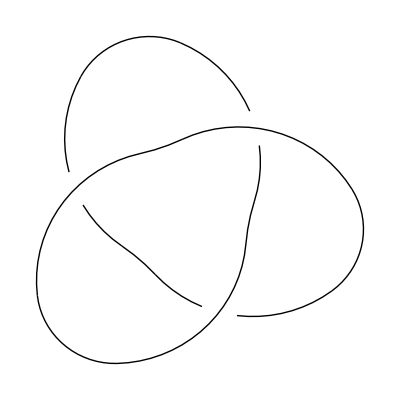

{{{1.},{5.56155,1.43845},{4.}},{{1.},{5.56155,4.,3.41421,1.43845,0.585786},{6.,5.23607,4.,2.,0.763932},{2.}},{{4.,3.41421,0.585786},{6.,6.,5.23607,2.,0.763932,0.},{3.,2.,-4.44089×10^-16}},{{6.},{3.}}}

(4 | 2 | 0 | 0 | 0 | 0
2 | 3 | -1 | 0 | 0 | 0
0 | -1 | 3 | 2 | 0 | 0
0 | 0 | 2 | 4 | 0 | 0
0 | 0 | 0 | 0 | 3 | 3
0 | 0 | 0 | 0 | 3 | 3)

```mathematica
unknot = PD[X[1,4,2,5],X[5,2,6,3],X[6,4,1,3]]
Show[DrawPD[unknot]]
qSpectraAllEigs[unknot]
qLapNew[unknot,0,-1] // MatrixForm
```